Practical-1
                                                                                                          BISECTION METHOD

(1)  Find a real root of the equation f(x)=log(1+x)-cos(x)=0 using bisection method in 10 iterations

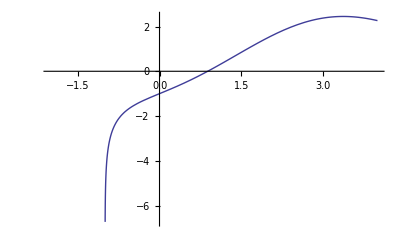

i | a_i | c_i | b_i | f[c_i]
0 | 0. | 0.5 | 1. | -0.4721174537822083
1 | 0.5 | 0.75 | 1. | -0.1720730809383982
2 | 0.75 | 0.875 | 1. | -0.0123881987409511
3 | 0.875 | 0.9375 | 1. | 0.06959340715288754
4 | 0.875 | 0.90625 | 0.9375 | 0.02843589519467271
5 | 0.875 | 0.890625 | 0.90625 | 0.007981228405989915
6 | 0.875 | 0.8828125 | 0.890625 | -0.00221425440755807
7 | 0.8828125 | 0.88671875 | 0.890625 | 0.002880808814339719
8 | 0.8828125 | 0.884765625 | 0.88671875 | 0.000332605881430581
9 | 0.8828125 | 0.8837890625 | 0.884765625 | -0.000940992314640399
10 | 0.8837890625 | 0.88427734375 | 0.884765625 | -0.0003042352019027028

Approximate root after10iterations is0.88427734375

Function value at approximated root,f[c]=-0.0003042352019027028

```mathematica
Bisection[a0_,b0_,n_,f_]:=
Module [{a = N[a0],b=N[b0]},
c=(a+b)/2;
i=0
If[f[a]*f[b]>0,Print["we cannot continue with the bisection method as ",f,"(a).",f,"(b)>=0"];Return[]];
output={{i,a,c,b,f[c]}};
While[i<n,If[Sign[f[b]]==Sign[f[c]],b=c,a=c;];c=(a+b)/2;i=i+1; output=Append[output, {i,a,c,b,f[c]}];];
Print[NumberForm[TableForm[output,TableHeadings->{None,{"i","a_i","c_i","b_i","f[c_i]"}}],16]];
Print["Approximate root after",i,"iterations is",NumberForm[c,16]];
Print["Function value at approximated root,f[c]=",NumberForm[f[c],16]];]
f[x_]:=Log[1+x]-Cos[x];
Plot[f[x],{x,-2,4}]
Bisection[0,1,10,f];
```

(2) Find one root of the function g(x)=x^3-5x+1,using Bisection Method Perform 12 iterations

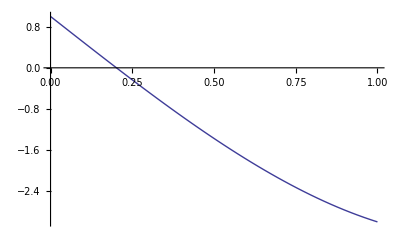

```mathematica
g[x_]:=x^3-5x+1;
Plot[g[x],{x,0,1}]
```

The root lies in the interval [0,1] now appply Bisection Method on the interval [3,4]

```mathematica
Bisection[0,1,5,g];
```

i | a_i | c_i | b_i | f[c_i]
0 | 0. | 0.5 | 1. | -1.375
1 | 0. | 0.25 | 0.5 | -0.234375
2 | 0. | 0.125 | 0.25 | 0.376953125
3 | 0.125 | 0.1875 | 0.25 | 0.069091796875
4 | 0.1875 | 0.21875 | 0.25 | -0.083282470703125
5 | 0.1875 | 0.203125 | 0.21875 | -0.007244110107421875

Approximate root after5iterations is0.203125

Function value at approximated root,f[c]=-0.007244110107421875

(3) Find  root of the function f(x)=cos[x]-xe^x,using Bisection Method Perform 5 iterations

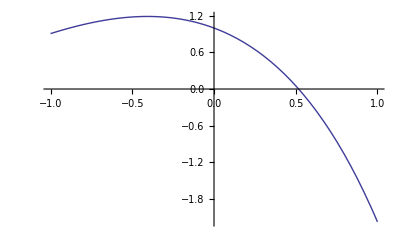

i | a_i | c_i | b_i | f[c_i]
0 | 0. | 0.5 | 1. | 0.05322192654030866
1 | 0.5 | 0.75 | 1. | -0.856061143585685
2 | 0.5 | 0.625 | 0.75 | -0.356690603889921
3 | 0.5 | 0.5625 | 0.625 | -0.1412937453091
4 | 0.5 | 0.53125 | 0.5625 | -0.04151221167208242
5 | 0.5 | 0.515625 | 0.53125 | 0.006475340827341247

Approximate root after5iterations is0.515625

Function value at approximated root,f[c]=0.006475340827341247

```mathematica
f[x_]:=Cos[x]-x Exp[x];
Plot[f[x],{x,-1,1}]
Bisection[0,1,5,f];
```

(4) Find an interval of unit length that Contains the smallest positive root of the function f(x)=x^4-3 x^2+x-10  perform 12 iterations of Bisection Method starting with resulted interval.

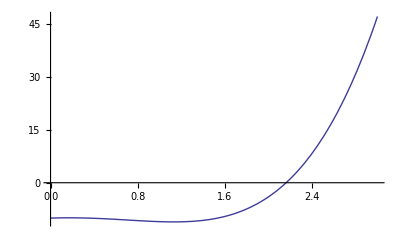

```mathematica
f[x_]=x^4-3 x^2+x-10;
Plot[f[x],{x,0,3}]
```

we can choose the interval of unit length [2,3] as the smallest positive root around 2.5, belongs to it

```mathematica
Bisection[2,3,12,f];
```

i | a_i | c_i | b_i | f[c_i]
0 | 2. | 2.5 | 3. | 12.8125
1 | 2. | 2.25 | 2.5 | 2.69140625
2 | 2. | 2.125 | 2.25 | -1.031005859375
3 | 2.125 | 2.1875 | 2.25 | 0.7297515869140625
4 | 2.125 | 2.15625 | 2.1875 | -0.1749410629272461
5 | 2.15625 | 2.171875 | 2.1875 | 0.2712278962135315
6 | 2.15625 | 2.1640625 | 2.171875 | 0.0466114915907383
7 | 2.15625 | 2.16015625 | 2.1640625 | -0.06454621977172792
8 | 2.16015625 | 2.162109375 | 2.1640625 | -0.00906291579303797
9 | 2.162109375 | 2.1630859375 | 2.1640625 | 0.01875037580703065
10 | 2.162109375 | 2.16259765625 | 2.1630859375 | 0.004837755005667077
11 | 2.162109375 | 2.162353515625 | 2.16259765625 | -0.002114073766389168
12 | 2.162353515625 | 2.1624755859375 | 2.16259765625 | 0.001361467229262558

Approximate root after12iterations is2.1624755859375

Function value at approximated root,f[c]=0.001361467229262558